```mathematica
ReverseSort@Last@With[{n=100,m=0},NestList[Block[{x=#},Scan[(If[x[[#]]>0,x[[#]]--;With[{j=RandomChoice[Delete[Range@n,#]]},x[[j]]++]])&,Range@n];x]&,ConstantArray[n,n],m]]
```

Append[{100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100}]

```mathematica
distbyRound=Parallelize[With[{n=100,m=100000},NestList[Block[{x=#},Scan[(If[x[[#]]>0,x[[#]]--;With[{j=RandomChoice[Delete[Range@n,#]]},x[[j]]++]])&,Range@n];x]&,ConstantArray[n,n],m]]];ReverseSort@Last@distbyRound
```

Parallelize::nopar1: With[{n=100,m=100000},NestList[Block[{x=#1},Scan[If[«2»]&,Range[n]];x]&,ConstantArray[n,n],m]] cannot be parallelized; proceeding with sequential evaluation.

{440,402,323,303,299,283,275,270,266,266,224,220,195,194,192,188,175,172,168,167,160,156,154,152,146,145,139,137,137,134,129,127,117,117,113,113,107,106,103,100,99,97,91,90,87,76,75,74,72,72,68,67,64,61,59,58,58,57,54,49,47,47,45,45,44,44,43,39,37,36,36,34,32,32,32,25,25,25,24,23,23,22,21,20,19,19,16,16,15,13,13,11,9,7,7,5,3,2,2,0}

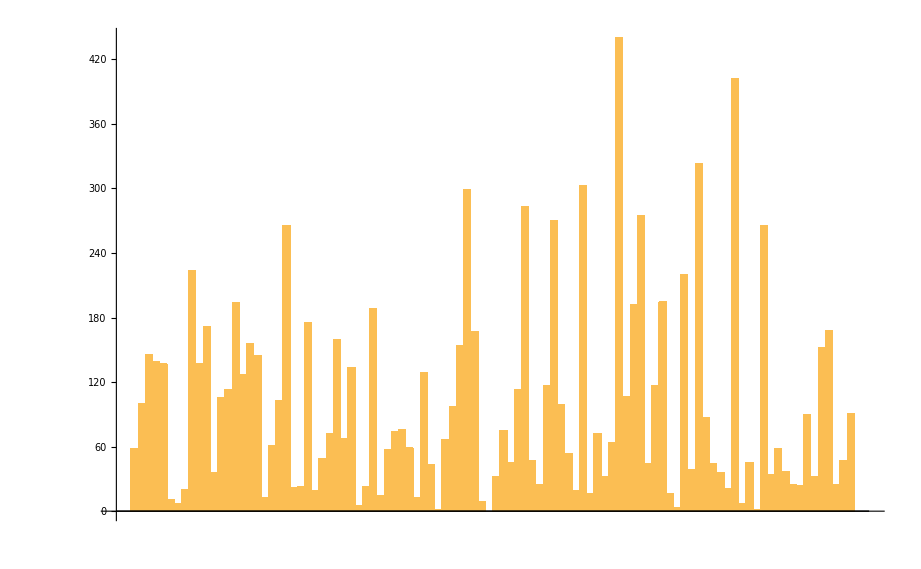

```mathematica
BarChart@Last@distbyRound
```

```mathematica
distbyPlayer=Transpose[distbyRound[[All,1;;100]]]
```

{1}
 |  |  |  |

```mathematica
Length@distbyPlayer[[1]]
```

Part::partd: Part specification distbyPlayer⟦1⟧ is longer than depth of object.

2

```mathematica
Length@dist
```

1001

```mathematica
Length@Transpose[dist[[1;;3]]]
```

100

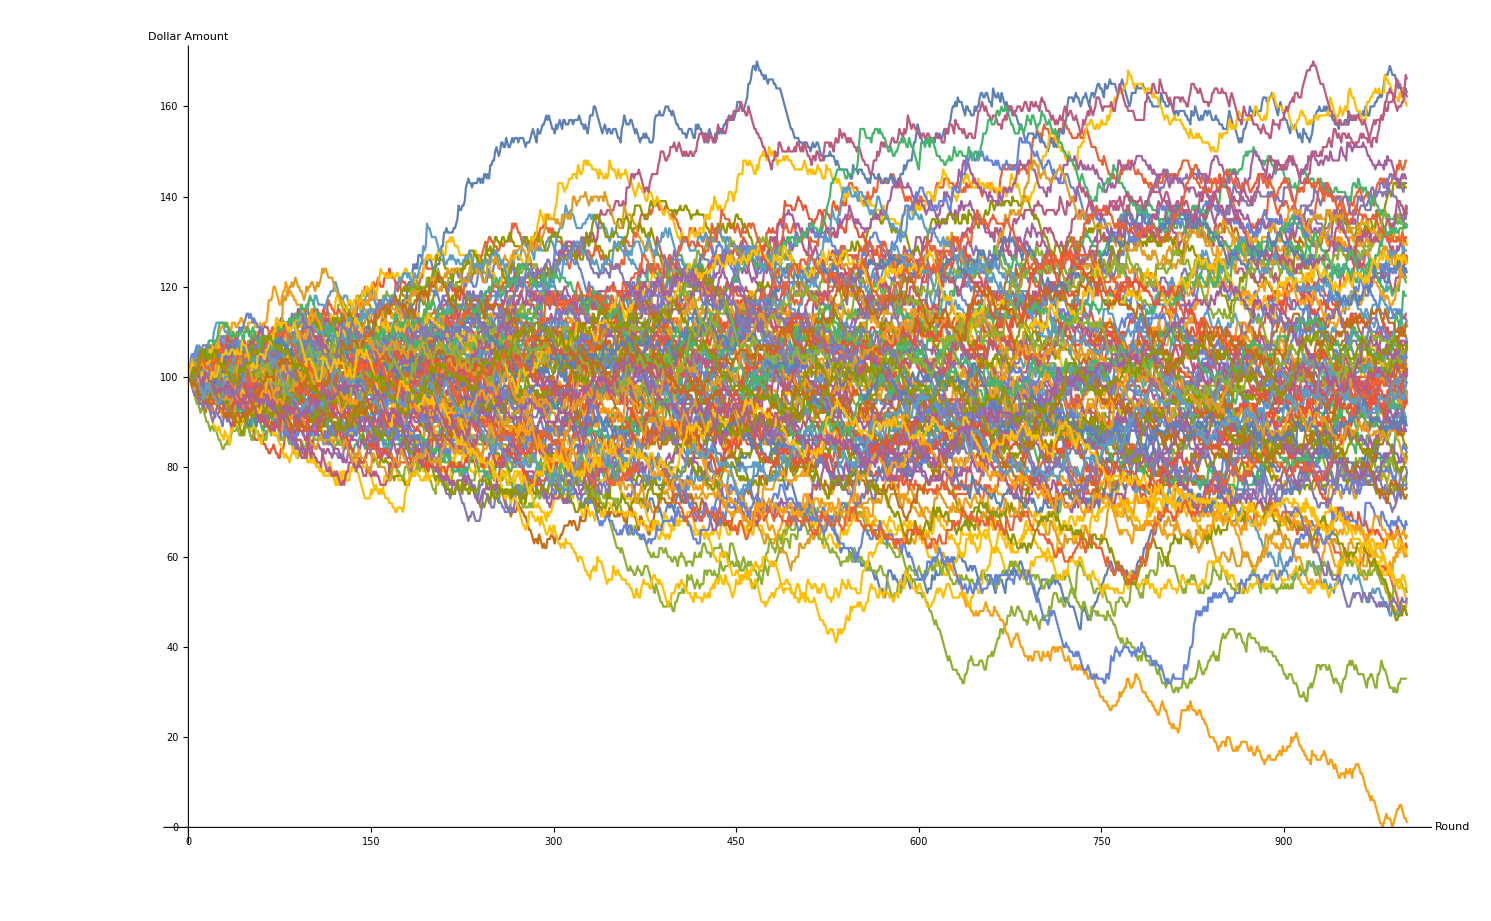

```mathematica
ListLinePlot[#&/@distbyPlayer,AxesLabel->{"Round","Dollar Amount"}]
```

```mathematica
Total@%137[[3]]
```

10000

```mathematica
100*100
```

10000

```mathematica
l={2,3,4}
```

{2,3,4}

```mathematica
Scan[Print[#^2]&,l]
```

4

9

16

```mathematica
l
```

{2,3,4}

```mathematica
Range@90
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90}

```mathematica
data=RandomVariate[UniformDistribution[{0,1}],100];
```

```mathematica
QuantilePlot[data,UniformDistribution[{0,1}]]
```

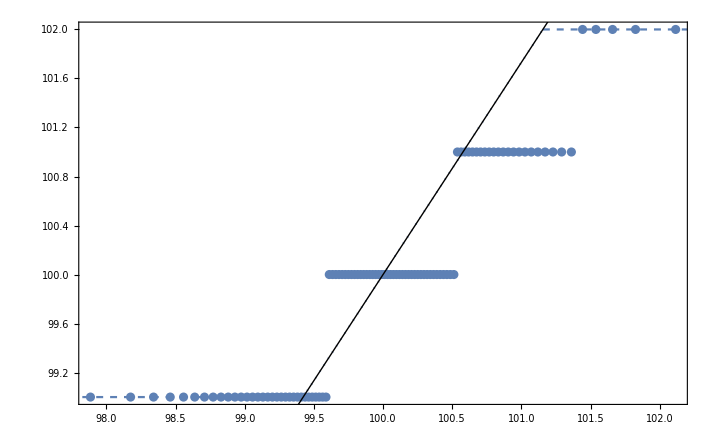

```mathematica
QuantilePlot[dist,UniformDistribution[{0,1}]]
```